# wbWeinSufCond wbWeinNecCond1 wbWeinNecCond2 wbWeinNecCond3

functions that filter the couplings according to the BFB conditions of Weinberg's model.

## Documentation

### Usage

wbWeinSufCond[list]

Filter the couplings according to the sufficient BFB conditions given in Refs. [1, 2]. The couplings are arranged in the following order: list = {a_1, a_2, a_3, b_1, b_2, b_3, c_1, c_2, c_3, d_1, d_2, d_3, ϵ}, with ϵ in radiansReturn: False | True.

wbWeinNecCond1[list]

Filter the couplings according to the 2HDM necessary BFB conditions (NCL1) given in Ref. [3]. The couplings in list are ordered according to the convention used in wbWeinSufCond. Return: False | True.

wbWeinNecCond2[list]

Filter the couplings according to additional necessary BFB conditions (NCL2-NCL3) given in Ref. [3]. The couplings in list are ordered according to the convention used in wbWeinSufCond. Return: False | True.

wbWeinNecCond3[list, list_1, list_2, list_3]

Filter the couplings by imposing additional necessary BFB conditions (NCL4) given in Ref. [3] via a scan over the orbit-space surface using the grids list_(1,2,3). The couplings in list are ordered according to the convention used in wbWeinSufCond. Return: False | True.

## Examples

To test usage examples make sure the package has been loaded:

```mathematica
wbLoadBinaries=True;(*wpCompTarget="C";*)
NotebookEvaluate[FileNameJoin[{ParentDirectory@NotebookDirectory[EvaluationNotebook[]],"StableWein.nb"}]]
```

### Basic Examples

Generate a set of couplings within the specified range and evaluate the BFB conditions:

```mathematica
couplSet=wbWeinParRndUniNec[]
```

{2.39985,0.58169,8.30693,9.61504,4.47864,14.403,13.3074,1.23243,14.5691,-7.99739,0.766801,3.98609,1.39189}

```mathematica
wbWeinSufCond[couplSet]
wbWeinNecCond1[couplSet]
wbWeinNecCond2[couplSet]
wbWeinNecCond3[couplSet,wbfaceListWein,wbθListWein,wbθListWein2]
```

True

True

True

«1 more identical outputs»

Fractions of points satisfying the BFB conditions:

```mathematica
data=ParallelTable[wbWeinParRndNec[10],{10^6}];
dataSuf=Pick[data,ParallelMap[wbWeinSufCond,data]];
dataNec1=Pick[data,ParallelMap[wbWeinNecCond1,data]];
dataNec2=Pick[dataNec1,ParallelMap[wbWeinNecCond2,dataNec1]];
dataNec3=Pick[dataNec2,ParallelMap[wbWeinNecCond3[#,wbfaceListWein,wbθListWein,wbθListWein2]&,dataNec2]];
Length/@{dataSuf,dataNec1,dataNec2,dataNec3}
PercentForm/@N[%/Length[data]]
```

{81237,92903,87876,87696}

{8.124%,9.29%,8.788%,8.77%}

All points that satisfy the sufficient BFB conditions also satisfy the necessary 2HDM conditions; however, points that satisfy the necessary 2HDM conditions do not necessarily satisfy the sufficient conditions:

```mathematica
Complement[dataSuf,dataNec1]//Length
Complement[dataNec1,dataSuf]//Length
Pick[dataSuf,ParallelMap[wbWeinNecCond1,dataSuf]]==Pick[dataNec1,ParallelMap[wbWeinSufCond,dataNec1]]
```

0

11666

True

To improve the accuracy of the scan over the orbit-space surface (function wbWeinNecCond3), the scanning grid can be refined by adjusting the parameter values of stepsWein. Note that increasing these values also increases the computation time. For most practical applications, the default settings (stepsWein = {17, 40, 0}) are sufficient; however, to achieve accuracy close 100% it may be necessary to increase them, for example to stepsWein = {30, 100, 50}.

By default, the global parameters (wbfaceListWein, wbθListWein, and wbθListWein2) specify the following numbers of grid points:

```mathematica
Length/@{wbfaceListWein,wbθListWein,wbθListWein2}
```

{5148,75113,0}

which enables relatively fast filtering of BFB-allowed points:

```mathematica
data=ParallelTable[wbWeinParRndNec[10],{10^3}];
Length[Pick[data,ParallelMap[wbWeinNecCond3[#,wbfaceListWein,wbθListWein,wbθListWein2]&,data]]]//AbsoluteTiming
```

{1.58847,345}

Using wbWeinGridGen, we increase the number of grid points:

```mathematica
stepsWein={27,80,30};
{wbfaceListWein,wbθListWein,wbθListWein2}=wbWeinGridGen[stepsWein];
```

Number of points in Weinberg's grids: {20000, 585497, 557}

which allows BFB-allowed points to be filtered more accurately, at the cost of increased computational time:

```mathematica
Length[Pick[data,ParallelMap[wbWeinNecCond3[#,wbfaceListWein,wbθListWein,wbθListWein2]&,data]]]//AbsoluteTiming
```

{28.7845,339}

Note that, in combination with wbWeinSufCond and wbWeinNecCond2, the function wbWeinNecCond3 yields highly accurate results even with the default grids, as can be seen in wbWeinUniBFBcheck.

### Scope

Couplings are generated in the range ∣coupling∣ ≤ 10 and are then filtered to retain only those that satisfy the relevant BFB conditions.

```mathematica
dataNec1=ParallelTable[testT=False; While[testT==False,paramT=wbWeinParRndNec[10]; testT=wbWeinNecCond1[paramT]]; paramT,{10^6}];
dataNec2=Pick[dataNec1,ParallelMap[wbWeinNecCond2,dataNec1]];
dataSuf=Pick[dataNec1,ParallelMap[wbWeinSufCond,dataNec1]];
Length/@{dataNec1,dataNec2,dataSuf}
PercentForm/@N[%/Length[dataNec1]]
```

{1000000,945194,872675}

{100%,94.52%,87.27%}

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3","ϵ"};
table1=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataNec1),TableHeadings->{parNames,{"Min","Max"}}]; 
table2=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataNec2),TableHeadings->{parNames,{"Min","Max"}}]; 
table3=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataSuf),TableHeadings->{parNames,{"Min","Max"}}];
Grid[#,Spacings->{0, 1}]&/@(Partition[#,1]&/@Transpose[{{"wbWeinNecCond1","wbWeinNecCond2","wbWeinSufCond"},{table1,table2,table3}}]);
Grid[{%},Spacings->{4, 0}]
```

wbWeinNecCond1
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.91 | 10.
b_2 | -9.81 | 10.
b_3 | -9.9 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10.
ϵ | 0. | 6.28 | wbWeinNecCond2
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.86 | 10.
b_2 | -9.78 | 10.
b_3 | -9.9 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10.
ϵ | 0. | 6.28 | wbWeinSufCond
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.78 | 10.
b_2 | -9.78 | 10.
b_3 | -9.74 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10.
ϵ | 0. | 6.28

Distribution of the couplings filtered with function wbWeinNecCond1 (green contour), function  wbWeinNecCond2 (blue dashed contour), and function  wbWeinSufCond (red dashed contour):

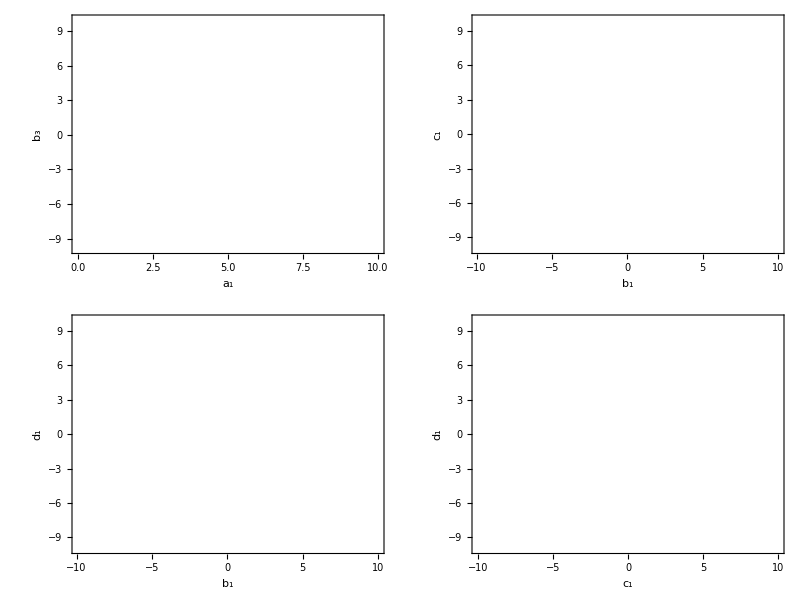

```mathematica
Table[Show[{ConvexHullMesh[dataNec1[[;;,xx]],MeshCellStyle->{1->{Darker[Green,0.2]},2->Opacity[0,Green]}],ConvexHullMesh[dataNec2[[;;,xx]],MeshCellStyle->{1->{Blue,Dashed},2->Opacity[0,Blue]}],ConvexHullMesh[dataSuf[[;;,xx]],MeshCellStyle->{1->{Red,Dashed},2->Opacity[0,Red]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->250,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]}],{xx,{{1,6},{4,7},{4,10},{7,10}}}];
Grid[Partition[%,2]]
```

Couplings are generated to satisfy the UNI and NCL1 conditions, and are then filtered to retain only those that also satisfy the NCL2-NCL3 or sufficient BFB conditions:

```mathematica
dataUniNec1=ParallelTable[testT=False; While[testT==False,paramT=wbWeinParRndUniNec[]; testT=wbWeinUNINec1Cond[paramT,8.*Pi]]; paramT,{10^6}];
dataUniNec2=Pick[dataUniNec1,ParallelMap[wbWeinNecCond2,dataUniNec1]];
dataUniSuf=Pick[dataUniNec1,ParallelMap[wbWeinSufCond,dataUniNec1]];
Length/@{dataUniNec1,dataUniNec2,dataUniSuf}
PercentForm/@N[%/Length[dataUniNec1]]
```

{1000000,753459,601594}

{100%,75.35%,60.16%}

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3","ϵ"};
table1=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniNec1),TableHeadings->{parNames,{"Min","Max"}}]; 
table2=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniNec2),TableHeadings->{parNames,{"Min","Max"}}]; 
table3=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniSuf),TableHeadings->{parNames,{"Min","Max"}}];
Grid[#,Spacings->{0, 1}]&/@(Partition[#,1]&/@Transpose[{{"wbWeinNecCond1","wbWeinNecCond2","wbWeinSufCond"},{table1,table2,table3}}]);
Grid[{%},Spacings->{4, 0}]
```

wbWeinNecCond1
 | Min | Max
a_1 | 0. | 8.37
a_2 | 0. | 8.37
a_3 | 0. | 8.37
b_1 | -7.88 | 15.4
b_2 | -7.88 | 15.42
b_3 | -7.72 | 15.57
c_1 | -15.79 | 15.91
c_2 | -15.67 | 15.62
c_3 | -15.99 | 15.84
d_1 | -8.19 | 8.11
d_2 | -8.19 | 8.08
d_3 | -8.27 | 8.07
ϵ | 0. | 6.28 | wbWeinNecCond2
 | Min | Max
a_1 | 0. | 8.37
a_2 | 0. | 8.37
a_3 | 0. | 8.37
b_1 | -7.37 | 15.4
b_2 | -7.45 | 15.42
b_3 | -7.35 | 15.57
c_1 | -15.2 | 15.42
c_2 | -15.14 | 15.45
c_3 | -15.99 | 15.22
d_1 | -8.06 | 7.93
d_2 | -8.05 | 7.91
d_3 | -8.2 | 7.91
ϵ | 0. | 6.28 | wbWeinSufCond
 | Min | Max
a_1 | 0. | 8.37
a_2 | 0. | 8.37
a_3 | 0. | 8.37
b_1 | -6.98 | 15.4
b_2 | -7.33 | 15.42
b_3 | -7.3 | 15.57
c_1 | -14.8 | 15.03
c_2 | -15.01 | 15.03
c_3 | -15.03 | 14.94
d_1 | -7.8 | 7.88
d_2 | -8.05 | 7.89
d_3 | -7.75 | 7.87
ϵ | 0. | 6.28

Distribution of the couplings satisfying UNI conditions and filtered with function wbWeinNecCond1 (green contour), function  wbWeinNecCond2 (blue dashed contour), and function  wbWeinSufCond (red dashed contour):

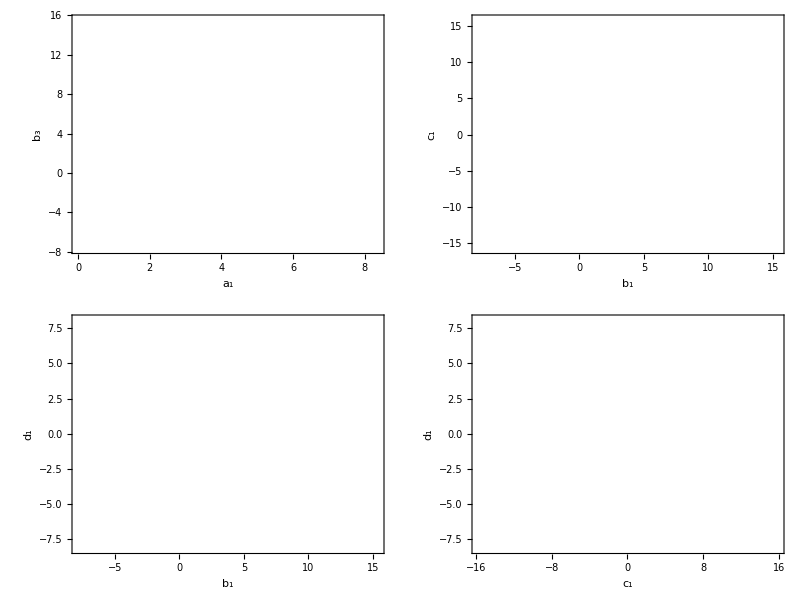

```mathematica
Table[Show[{ConvexHullMesh[dataUniNec1[[;;,xx]],MeshCellStyle->{1->{Darker[Green,0.2]},2->Opacity[0,Green]}],ConvexHullMesh[dataUniNec2[[;;,xx]],MeshCellStyle->{1->{Blue,Dashed},2->Opacity[0,Blue]}],ConvexHullMesh[dataUniSuf[[;;,xx]],MeshCellStyle->{1->{Red,Dashed},2->Opacity[0,Red]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->250,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]}],{xx,{{1,6},{4,7},{4,10},{7,10}}}];
Grid[Partition[%,2]]
```

### Options

## Source & Additional Information

### Related Symbols

wbWeinParRnd ▪ wbWeinParRndNec ▪ wbWeinParRndUni ▪ wbWeinParRndUniNec ▪ wbWeinUNICond ▪ wbWeinUNINec1Cond ▪ wbWeinUniBFBcheck

### References

[1] R. Boto, J.C. Romao and J.P. Silva, Bounded from below conditions on a class of symmetry constrained 3HDM, Phys. Rev. D 106 (2022) no.11, 115010 https://doi.org/10.1103/PhysRevD.106.115010 [arXiv:2208.01068 [hep-ph]].

[2] B. Grzadkowski, O.M. Ogreid and P. Osland, Natural Multi-Higgs Model with Dark Matter and CP Violation, Phys. Rev. D 80 (2009), 055013 https://doi.org/10.1103/PhysRevD.80.055013 [arXiv:0904.2173 [hep-ph]].

[3] D. Jurčiukonis, L. Lavoura and A. Milagre, Assessing boundedness from below in the Z_2 x Z_2-symmetric three-Higgs-doublet model: algorithm and machine learning, arXiv:2603.xxxxx [hep-ph].